#### 10.04.21 - Расчёт ошибки кумулянта прямоугольного Изинга при разных отношениях сторон

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\user\Documents\Wolfram Mathematica\Проект\Расчёты .nb

```mathematica
data = Import["results.txt", "table"]
```

{{50,0.25,1,0.109901,0.00462847,0.0279148,0.00212686,0.229605},{50,0.5,1,0.141223,0.00422358,0.0374659,0.00187789,0.373811},{50,0.75,1,0.143292,0.0042087,0.0377988,0.00180791,0.386359},{100,0.25,1,0.0890685,0.00405307,0.018081,0.00161062,0.240281},{100,0.5,1,0.115757,0.00358826,0.0261556,0.00130813,0.349347},{100,0.75,1,0.118994,0.00358253,0.0265074,0.00162272,0.375988}}

data[...][1] - L
data[...][2] - CoefXY
data[...][3] - OpenBorderQ (1 - Yes, 0 - No)
data[...][4] - ⟨m2⟩
data[...][5] - σ(m2)
data[...][6] - ⟨m4⟩
data[...][7] - σ(m4)
data[...][8] - U_4

#### Реализация расчёта ошибки:

1. Генерация набора из 1000 значений намагниченностей (второй и четвёртой степени) (средним в распределении является средняя намагниченность, а С.К.О. - её ошибка) и набора кумулянтов из первых двух наборов

```mathematica
dM2 = RandomVariate[NormalDistribution[data[[1]][[4]], data[[1]][[5]]],1000];
dM4 = RandomVariate[NormalDistribution[data[[1]][[6]], data[[1]][[7]]],1000];
dU4 = 1 - dM4 / (3 * dM2^2);
```

Так выглядит гистограмма распределения кумулянта

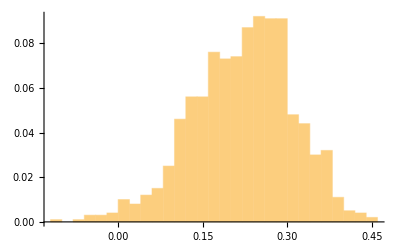

```mathematica
Histogram[dU4, Automatic, "Probability"]
```

На основе гистограммы задаём распределение кумулянта и находит его отклонение

```mathematica
StandardDeviation[HistogramDistribution[dU4]]
```

0.0889934

#### Полуавтоматизированный алгоритм для задания набора точек и их ошибок:

```mathematica
Ls={50,100};
FullData={};
Do[
lData=Select[data, #[[1]]==L&];
line={};
For [i=1, i≤Length[lData],i++,
dM2 = RandomVariate[NormalDistribution[lData[[i]][[4]], lData[[i]][[5]]],1000];
dM4 = RandomVariate[NormalDistribution[lData[[i]][[6]], lData[[i]][[7]]],1000];
dU4 = 1 - dM4 / (3 * dM2^2);
dot={{lData[[i]][[2]], lData[[i]][[8]]},ErrorBar[StandardDeviation[HistogramDistribution[dU4]]]};
AppendTo[line,dot];
];
AppendTo[FullData,line];
,{L,Ls}]
```

```mathematica
Needs["ErrorBarPlots`"]
```

#### График для первых шести расчётов (L=50, 100, AspectRatio=1/4, 1/2 3/4)

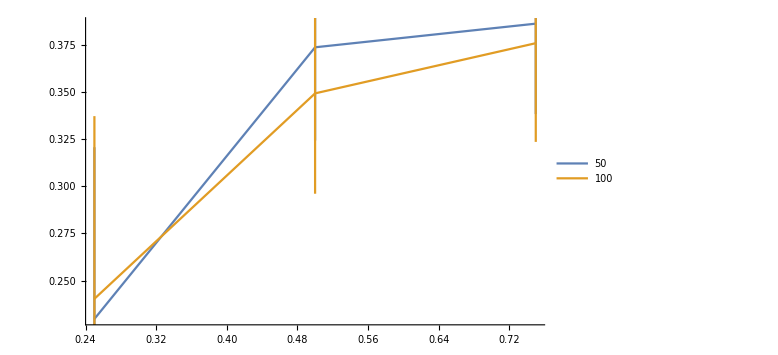

```mathematica
ErrorListPlot[FullData, PlotLegends->Ls, ImageSize->Large, Joined->True]
```

#### Как и ожидалось, погрешности слишком большие -> требуется увеличение времени работы алгоритма

#### 10.04.2021 - Расчёт при новых данных

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\user\Documents\Wolfram Mathematica\Проект\Расчёты .nb

```mathematica
data=Import["results2.txt","table"]
```

{{50,0.25,1,0.109567,0.0012553,0.0277495,0.000555247,0.2295},{50,0.5,1,0.139515,0.00153194,0.0380324,0.000659079,0.348689},{50,0.75,1,0.143534,0.00168099,0.0379902,0.000750858,0.385329},{100,0.25,1,0.0873405,0.00117321,0.0177195,0.000429325,0.225718},{100,0.5,1,0.11418,0.00149426,0.0251839,0.000440689,0.356097},{100,0.75,1,0.120044,0.00115745,0.0260882,0.000407595,0.396548},{200,0.25,1,0.0725037,0.000832001,0.0118999,0.000244944,0.245425},{200,0.5,1,0.09441,0.00115648,0.0172971,0.000302764,0.353132},{400,0.25,1,0.0614871,0.000832213,0.00863458,0.000227393,0.238706},{200,0.75,1,0.0983118,0.000970211,0.0178971,0.00028873,0.382767},{400,0.5,1,0.0782073,0.000808983,0.0118324,0.000192356,0.355153},{400,0.75,1,0.0841728,0.000761902,0.0128747,0.000193869,0.394277},{}}

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Ls={50,100,200,400};
FullData={};
Do[
lData=Select[data, #[[1]]==L&];
line={};
For [i=1, i≤Length[lData],i++,
dM2 = RandomVariate[NormalDistribution[lData[[i]][[4]], lData[[i]][[5]]],1000];
dM4 = RandomVariate[NormalDistribution[lData[[i]][[6]], lData[[i]][[7]]],1000];
dU4 = 1 - dM4 / (3 * dM2^2);
dot={{lData[[i]][[2]], lData[[i]][[8]]},ErrorBar[StandardDeviation[HistogramDistribution[dU4]]]};
AppendTo[line,dot];
];
AppendTo[FullData,line];
,{L,Ls}]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
FullData
```

{{{{0.25,0.2295},ErrorBar[0.0237283]},{{0.5,0.348689},ErrorBar[0.018332]},{{0.75,0.385329},ErrorBar[0.0194156]}},{{{0.25,0.225718},ErrorBar[0.0290121]},{{0.5,0.356097},ErrorBar[0.0204822]},{{0.75,0.396548},ErrorBar[0.0149492]}},{{{0.25,0.245425},ErrorBar[0.0231351]},{{0.5,0.353132},ErrorBar[0.0193881]},{{0.75,0.382767},ErrorBar[0.0161074]}},{{{0.25,0.238706},ErrorBar[0.0290816]},{{0.5,0.355153},ErrorBar[0.0167208]},{{0.75,0.394277},ErrorBar[0.0144576]}}}

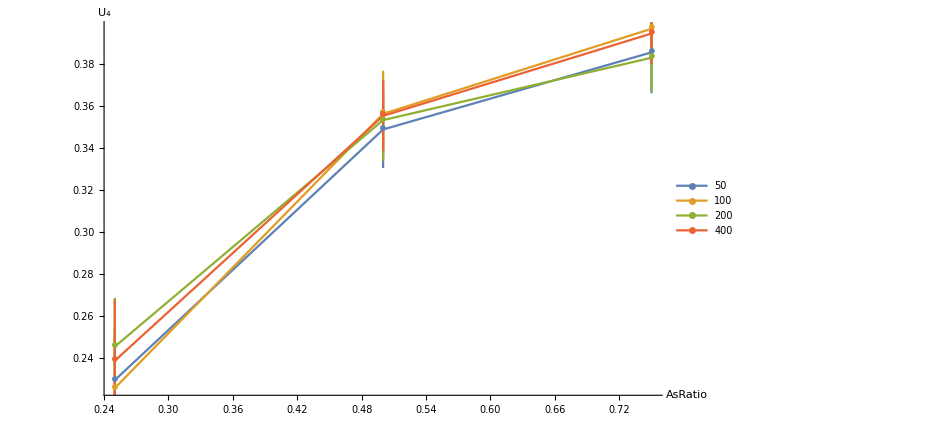

```mathematica
ErrorListPlot[FullData, PlotLegends->Ls, ImageSize->700, Joined->True, PlotMarkers->{•,20}, AxesLabel->{Style["AsRatio",FontSize->16], Style["U_4",FontSize->16]}]
```

#### 12.04.2021 (Расчёт кумулянтов для модели с PBC)

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["resultsPBC.txt","table"]
```

{{50,0.25,0,0.269794,0.00232804,0.127142,0.00158263,0.417757},{50,0.5,0,0.312071,0.00246671,0.139531,0.00144705,0.522426},{50,0.75,0,0.30228,0.00192382,0.126702,0.00121336,0.537786},{100,0.25,0,0.228786,0.00271831,0.0901712,0.00164021,0.425766},{100,0.5,0,0.259139,0.0017056,0.0962136,0.000915685,0.522416},{100,0.75,0,0.251772,0.00191746,0.0872005,0.000947267,0.541453},{200,0.25,0,0.192994,0.00203884,0.0637276,0.000870031,0.429682},{200,0.5,0,0.216068,0.00150092,0.0668941,0.000782415,0.522377},{200,0.75,0,0.20914,0.00132096,0.0605322,0.000567653,0.538694},{400,0.25,0,0.159846,0.00153953,0.0442979,0.000623266,0.42209},{400,0.5,0,0.179423,0.00121218,0.0468893,0.000458924,0.514494}}

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Ls={50,100,200,400};
FullData={};
Do[
lData=Select[data, #[[1]]==L&];
line={};
For [i=1, i≤Length[lData],i++,
dM2 = RandomVariate[NormalDistribution[lData[[i]][[4]], lData[[i]][[5]]],1000];
dM4 = RandomVariate[NormalDistribution[lData[[i]][[6]], lData[[i]][[7]]],1000];
dU4 = 1 - dM4 / (3 * dM2^2);
dot={{lData[[i]][[2]], lData[[i]][[8]]},ErrorBar[StandardDeviation[HistogramDistribution[dU4]]]};
AppendTo[line,dot];
];
AppendTo[FullData,line];
,{L,Ls}]
```

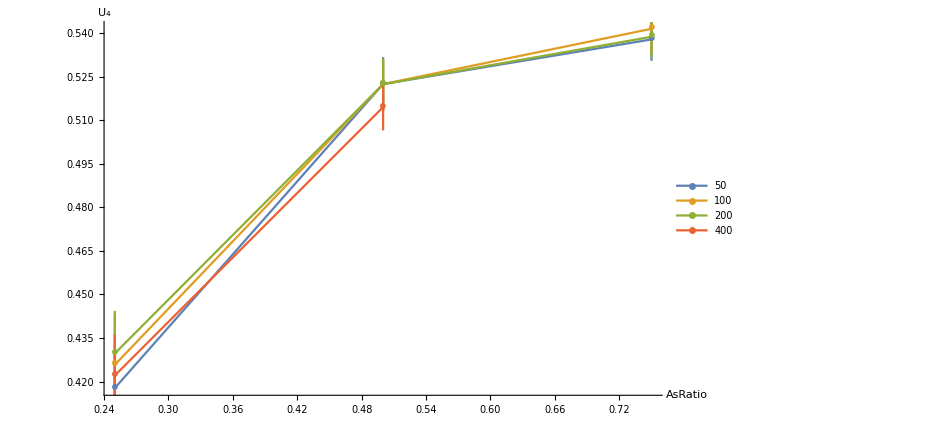

```mathematica
ErrorListPlot[FullData, PlotLegends->Ls, ImageSize->700, Joined->True, PlotMarkers->{•,20}, AxesLabel->{Style["AsRatio",FontSize->16], Style["U_4",FontSize->16]}]
```